```mathematica
plotWithExtrema[f_,{xmin_,xmax_}]:=Module[{minima,maxima,extrema},extrema=FindArgMinOrMax[f,{x,xmin,xmax}];
minima=Select[extrema,Last[#]=="min"&];
maxima=Select[extrema,Last[#]=="max"&];
Plot[f,{x,xmin,xmax},Epilog->{Red,PointSize[0.02],Tooltip[Point[{#,f/. x->#}],{#,"Minimum"}]&/@minima,Blue,Tooltip[Point[{#,f/. x->#}],{#,"Maksimum"}]&/@maxima}]]

(*Funkcja do znajdowania minimów i maksimów*)

FindArgMinOrMax[f_,{x_,xmin_,xmax_}]:=Module[{df,zeros,extremapoints},df=D[f,x];
zeros=x/. NSolve[df==0&&xmin<=x<=xmax,x];
extremapoints={{#,"min"}&/@Select[zeros,D[df,{x,2}]>0],{#,"max"}&/@Select[zeros,D[df,{x,2}]<0]};
Flatten[extremapoints,1]]

(*Rysowanie stycznej do funkcji w zadanym miejscu*)

plotTangent[f_,{x0_,xmin_,xmax_}]:=Module[{tangent,intersection},tangent=Normal@Series[f,{x,x0,1}];
intersection={x0,f/. x->x0};
Plot[{f,tangent},{x,xmin,xmax},Epilog->{PointSize[0.02],Red,Tooltip[Point[intersection],{"Przecięcie",intersection}]}]]

(*Liczenie pola pod wykresem*)

areaUnderCurve[f_,{x_,xmin_,xmax_}]:=Module[{area},area=NIntegrate[f,{x,xmin,xmax}];
Plot[f,{x,xmin,xmax},Filling->Axis,PlotLabel->Row[{"Pole = ",area}]]]
```

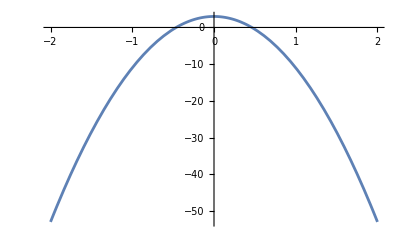

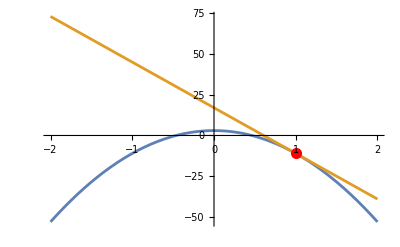

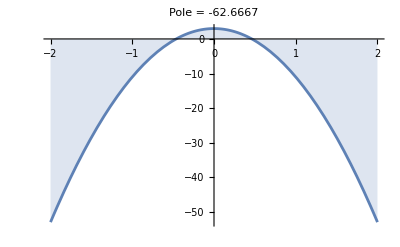

```mathematica
f[x_]:=x^2-15 x^2+3;

plotWithExtrema[f[x],{-2,2}]
plotTangent[f[x],{1,-2,2}]
areaUnderCurve[f[x],{x,-2,2}]
```